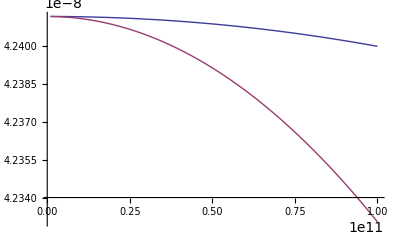

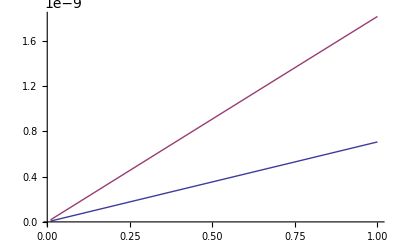

```mathematica
e0=8.85*10^-12;

alphaSph[ν_,σ_,R_]=(4π*R^3)/3((-ⅈ*σ)/(2π*ν*e0))/(1+1/3((-ⅈ*σ)/(2π*ν*e0)));(**)

alphaHollSph[ν_,σ_,R_,r_]=3(4π*R^3)/3((3-2(ⅈ*σ)/(2π*ν*e0))(ⅈ*σ)/(2π*ν*e0)(r^3/R^3-1))/((3-(ⅈ*σ)/(2π*ν*e0))*(3-2(ⅈ*σ)/(2π*ν*e0))+2 r^3/R^3(σ/(2π*ν*e0))^2);(*(4π*R^3)/3*)
sigma=1000;
radius=0.0015;
radius2=radius*0.8;
(*Plot[{Re[alphaSph[ν,sigma,radius]],-Im[alphaSph[ν,sigma,radius]]},{ν,0.01*10^9,500*10^9}]
Plot[{Re[alphaHollSph[ν,sigma,radius,radius2]],-Im[alphaHollSph[ν,sigma,radius,radius2]]},{ν,0.01*10^9,500*10^9}]*)

Plot[{Re[alphaSph[ν,sigma,radius]],Re[alphaHollSph[ν,sigma,radius,radius2]]},{ν,1*10^9,100*10^9},PlotRange-> All]
Plot[{-Im[alphaSph[ν,sigma,radius]],-Im[alphaHollSph[ν,sigma,radius,radius2]]},{ν,1*10^9,100*10^9}]
```

```mathematica
Plot[{Re[alphaSph[ν,sigma,radius]],Re[alphaHollSph[ν,sigma,radius,radius2]]},{ν,1*10^9,100*10^9},PlotRange-> All]
```

-Graphics-

```mathematica
alphaSph[16.5*10^9,100,1.5*10^-3]
```

4.23794×10^-8-1.1665×10^-9 ⅈ

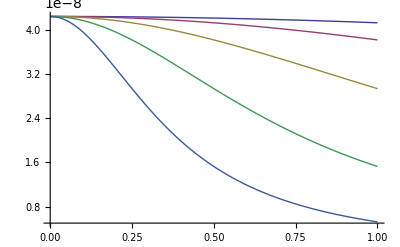

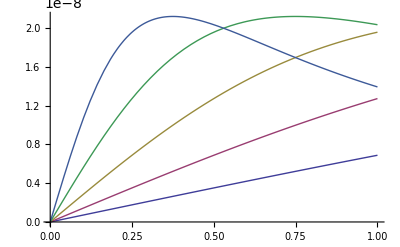

```mathematica
Plot[{Re[alphaSph[ν,sigma,radius]],Re[alphaSph[ν,sigma/2,radius]],Re[alphaSph[ν,sigma/4,radius]],Re[alphaSph[ν,sigma/8,radius]],Re[alphaSph[ν,sigma/16,radius]]},{ν,1*10^9,1000*10^9},PlotRange-> All]

Plot[{-Im[alphaSph[ν,sigma,radius]],-Im[alphaSph[ν,sigma/2,radius]],-Im[alphaSph[ν,sigma/4,radius]],-Im[alphaSph[ν,sigma/8,radius]],-Im[alphaSph[ν,sigma/16,radius]]},{ν,1*10^9,1000*10^9},PlotRange-> All]
```

0.0015

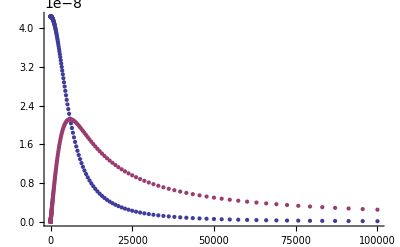

```mathematica
MinFrq=9;
MaxFrq=14;
points=250;
radius
ReAlphaTh=Table[0,{i,points}];
ImAlphaTh=Table[0,{i,points}];
sigma=1000;
For[i=1,i≤points,
(
nnu=10^MinFrq*10^((MaxFrq-MinFrq)/(points-1)*(i-1));
ReAlphaTh[[i]]={N[nnu/10^9],Re[alphaSph[nnu,sigma,radius]]};
ImAlphaTh[[i]]={N[nnu/10^9],-Im[alphaSph[nnu,sigma,radius]]};

);

i++];
ListPlot[{ReAlphaTh,ImAlphaTh}]
```

```mathematica
Export["D:\\MOIDOK\\ReAlpha-sphere-D3mm-sig1000"<>".xls",ReAlphaTh]
Export["D:\\MOIDOK\\ImAlpha-sphere-D3mm-sig1000"<>".xls",ImAlphaTh]
```

D:\MOIDOK\ReAlpha-sphere-D3mm-sig1000.xls

D:\MOIDOK\ImAlpha-sphere-D3mm-sig1000.xls

0.0015

100

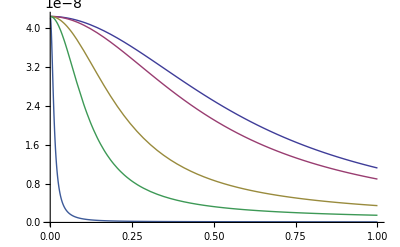

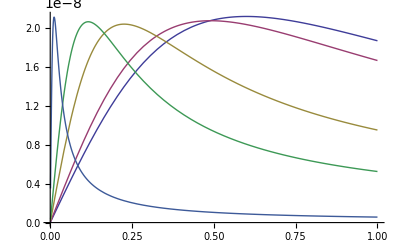

```mathematica
radius
sigma=100
Plot[{Re[alphaHollSph[ν,sigma,radius,radius*0]],Re[alphaHollSph[ν,sigma,radius,radius*0.5]],Re[alphaHollSph[ν,sigma,radius,radius*0.8]],Re[alphaHollSph[ν,sigma,radius,radius*0.9]],Re[alphaHollSph[ν,sigma,radius,radius*0.99]]},{ν,1*10^9,1000*10^9},PlotRange-> All]

Plot[{-Im[alphaHollSph[ν,sigma,radius,radius*0]],-Im[alphaHollSph[ν,sigma,radius,radius*0.5]],-Im[alphaHollSph[ν,sigma,radius,radius*0.8]],-Im[alphaHollSph[ν,sigma,radius,radius*0.9]],-Im[alphaHollSph[ν,sigma,radius,radius*0.99]]},{ν,1*10^9,1000*10^9},PlotRange-> All]
```

```mathematica
alphaHollSph[10*10^9,sigma,radius,radius*0]
alphaSph[10*10^9,sigma,radius]
```

4.23997×10^-8-7.07306×10^-10 ⅈ

4.23997×10^-8-7.07306×10^-10 ⅈ

0.0015

100

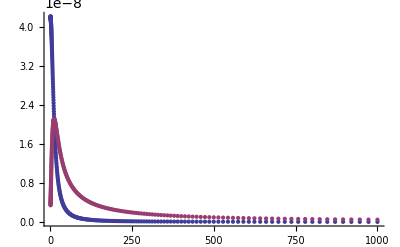

```mathematica
MinFrq=9;
MaxFrq=12;
points=250;
radius
sigma=100

α=0.99;

ReAlphaTh=Table[0,{i,points}];
ImAlphaTh=Table[0,{i,points}];

For[i=1,i≤points,
(
nnu=10^MinFrq*10^((MaxFrq-MinFrq)/(points-1)*(i-1));
ReAlphaTh[[i]]={N[nnu/10^9],Re[alphaHollSph[nnu,sigma,radius,α*radius]]};
ImAlphaTh[[i]]={N[nnu/10^9],-Im[alphaHollSph[nnu,sigma,radius,α*radius]]};

);

i++];
ListPlot[{ReAlphaTh,ImAlphaTh}]
```

```mathematica
Export["D:\\MOIDOK\\ReAlpha-HollSphere-D3mm-d099D-sig100"<>".xls",ReAlphaTh]
Export["D:\\MOIDOK\\ImAlpha-HollSphere-D3mmd-d099D-sig100"<>".xls",ImAlphaTh]
```

D:\MOIDOK\ReAlpha-HollSphere-D3mm-d099D-sig100.xls

D:\MOIDOK\ImAlpha-HollSphere-D3mmd-d099D-sig100.xls

```mathematica
Simplify[alphaHollSph[x,y,z,v]]
```

((0.+2.25989×10^11 ⅈ) (3. x-(0.+3.59672×10^10 ⅈ) y) y z^3 (v^3-1. z^3))/(6.4682×10^20 v^3 y^2+(9. x^2-(0.+1.61852×10^11 ⅈ) x y-6.4682×10^20 y^2) z^3)

0.0005

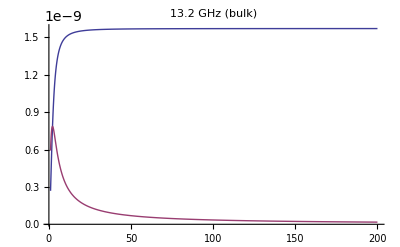

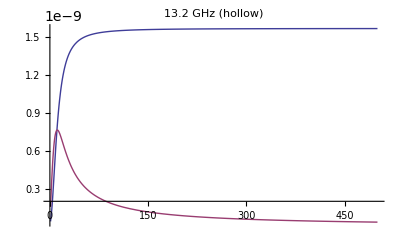

```mathematica
nu=13.2*10^9;
radius=0.0005

(*Plot[{Re[alphaSph[nu,σ,radius]],Re[alphaSph[nu,σ,2radius]],Re[alphaSph[nu,σ,3radius]],Re[alphaSph[nu,σ,4radius]],Re[alphaSph[nu,σ,5radius]]},{σ,1,20},PlotRange-> All]

Plot[{-Im[alphaSph[nu,σ,radius]],-Im[alphaSph[nu,σ,2radius]],-Im[alphaSph[nu,σ,3radius]],-Im[alphaSph[nu,σ,4radius]],-Im[alphaSph[nu,σ,5radius]]},{σ,1,20},PlotRange-> All]
*)


Plot[{Re[alphaSph[nu,σ,radius]],-Im[alphaSph[nu,σ,radius]]},{σ,1,200},PlotRange-> All,PlotLabel-> ToString[nu/10^9]"GHz (bulk)"]


Plot[{Re[alphaHollSph[nu,σ,radius,radius*0.9]],-Im[alphaHollSph[nu,σ,radius,radius*0.9]]},{σ,1,500},PlotRange-> All,PlotLabel-> ToString[nu/10^9]"GHz (hollow)"]
```

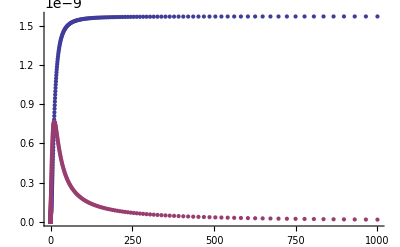

```mathematica
MinSig=-5;
MaxSig=3;
points=512;
frq=13.22*10^9;

ReAlphaTh=Table[0,{i,points}];
ImAlphaTh=Table[0,{i,points}];

For[i=1,i≤points,
(
sigma=10^MinSig*10^((MaxSig-MinSig)/(points-1)*(i-1));
ReAlphaTh[[i]]={N[sigma],Re[alphaHollSph[frq,sigma,radius,0.9*radius]]};
ImAlphaTh[[i]]={N[sigma],-Im[alphaHollSph[frq,sigma,radius,0.9*radius]]};

);

i++];
ListPlot[{ReAlphaTh,ImAlphaTh}]
```

```mathematica
Export["D:\\MOIDOK\\ReAlpha-HollSphere-D3mm-d09D-frq13p2"<>".xls",ReAlphaTh]
Export["D:\\MOIDOK\\ImAlpha-HollSphere-D3mmd-d09D-frq13p2"<>".xls",ImAlphaTh]
```

D:\MOIDOK\ReAlpha-HollSphere-D3mm-d09D-frq13p2.xls

D:\MOIDOK\ImAlpha-HollSphere-D3mmd-d09D-frq13p2.xls

```mathematica
radius
```

0.0005